0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.92

0.94

0.96

0.98

1.

1.02

1.04

1.06

1.08

1.1

1.12

1.14

1.16

1.18

1.2

1.22

1.24

1.26

1.28

1.3

1.32

1.34

1.36

1.38

1.4

1.42

1.44

1.46

1.48

1.5

1.52

1.54

1.56

1.58

1.6

1.62

1.64

1.66

1.68

1.7

1.72

1.74

1.76

1.78

1.8

1.82

1.84

1.86

1.88

1.9

1.92

1.94

1.96

1.98

2.

2.02

2.04

2.06

2.08

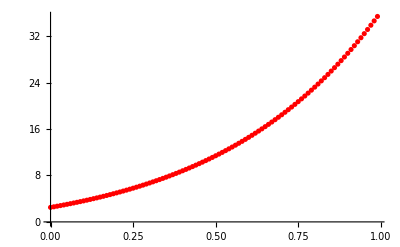

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
(* t from 0 to 3 (including) *)
f[t_,u_] := t+2u + 5;
iValue = 2.5;

(* Явен метод на Ойлер. Неговата ЛГА е O(H) *)
ExplicitEuiler[f_,y0_,t0_,h_,T_] := (
Block[{n,y,i,t},{
n = N[T/h];
y = Table[0,{i,0,n}];
t = Table[0,{i,0,n}];
y[[1]] =y0;
t[[1]] = t0;
For[i=1,i<=n,++i,
y[[i+1]] = y[[i]] + h(t[[i]]+2y[[i]]+5);
t[[i+1]] = t[[i]]+0.02;
];
Table[{h(i-1),y[[i]]},{i,0,n}]
}]
);

sol = ExplicitEuiler[f,iValue,0.1,0.01,1];
ListPlot[sol,PlotStyle->Red]
```